```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4GatesHarvard.csv"]; (*Imported gates from Qiskit*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
(*BlockadeRadius->Sqrt[2],*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
RydDev[Gates][[All,1]]
```

-Graphics3D-

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAPDCG_(q1$_Integer,q2$_Integer),SWAPDCH_(q1$_Integer,q2$_Integer),InstaSWAP_(q1_,q2_),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$971334,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$971334[{p$,q$}],CZG_(p$_Integer,q$_Integer)/;blockadeCheck$971334[{p$,q$}],CZH_(p$_Integer,q$_Integer)/;blockadeCheck$971334[{p$,q$}],CCZ_(i$_,j$_,k$_)/;blockadeCheck$971334[{i$,j$}]/;blockadeCheck$971334[{j$,k$}]/;blockadeCheck$971334[{k$,i$}],C_c$_[Z_t$__]/;blockadeCheck$971334[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$971334[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$971334[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[CZG, 0,1]},RydDev,ReplaceAliases->True]]
```

{UNonNorm_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7]}

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
```

```mathematica
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Pelegri CZ*)
MoveTime=500;
SU4GateGINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Levine CZ*)
SU4GateHINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Pelegri CZ*)
SU4GateGDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCG], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Levine CZ*)
SU4GateHDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCH], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Pelegri CZ*)
SU4GateGMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZG,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Levine CZ*)
SU4GateHMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZH,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*SU4Gate[data[[400;;1000]][[112]],0,1]*)
```

```mathematica
(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

```mathematica
(*Generate a layer of gates for building a QV circuit*)
QVLayerGA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCG, RQs[[n+1]],3]},SU4GateGDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCG, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateGMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];

QVLayerHA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCH, RQs[[n+1]],3]},SU4GateHDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCH, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateHMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];
```

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},RydDev]]
```

{Deph_0[0.000167757],Deph_1[0.000167757],Deph_2[0.000167757],Deph_3[0.000167757],Deph_4[0.000167757],Deph_5[0.000167757],Deph_6[0.000167757],Deph_7[0.000167757],Deph_8[0.000167757],Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}

```mathematica
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Table[RQS=NRandQbits[NQ];Layer=Which[StringContainsQ[ConnectivityRule,"GA2A"],QVLayerGA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GSWAP"],QVLayerGSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GMove"],QVLayerGMove[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HA2A"],QVLayerHA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HSWAP"],QVLayerHSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HMove"],QVLayerHMove[DataSet,NQ,RQS,i]];
(*Print["# Qubits, ",NQ," # Gates per Layer, ",Length[Layer]]*);Flatten[Layer],{i,0,NQ-1,1}]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];


(*GA2AQV=QVCalc[data,9,200,"GA2A"]
GSWAPQV=QVCalc[data,9,200,"GSWAP"]*)
(*HA2AQV=QVCalc[data,9,200,"HA2A"]
HSWAPQV=QVCalc[data,9,200,"HSWAP"]*)

(*GMoveQV=QVCalc[data,9,200,"GMove"]*)
HMoveQV=QVCalc[data,9,200,"HMove"]
DestroyAllQuregs[];
```

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,256,256}

{Layer,9,512,512}

{{{2,0.744392,0.0124362},{2,0.797483,0.0133224},{2,0.0665743,0.0000456121}},{{3,0.793556,0.0119623},{3,0.852579,0.0128443},{3,0.0692355,0.0000489435}},{{4,0.766592,0.00685286},{4,0.835407,0.00746632},{4,0.0823734,0.0000684651}},{{5,0.775042,0.00506225},{5,0.84956,0.00553435},{5,0.0877184,0.0000754245}},{{6,0.752821,0.00340401},{6,0.844183,0.00380469},{6,0.108227,0.0000802885}},{{7,0.748289,0.00243354},{7,0.846299,0.00275703},{7,0.115809,0.000096641}},{{8,0.711178,0.00158695},{8,0.829964,0.00187315},{8,0.143118,0.0000982157}},{{9,0.698812,0.00119924},{9,0.824981,0.00140833},{9,0.152935,0.0000917474}}}

```mathematica
GA2AQV={{{2,0.7401162361932938,0.012637402938430044},{2,0.7964910548441765,0.013615081829584806},{2,0.07076106272829308,0.00009496551045323869}},{{3,0.7808532734596401,0.01123275654433871},{3,0.8447396543799234,0.01215058728845331},{3,0.07562931638415364,0.00011586005035170743}},{{4,0.7572166665746672,0.0061283295238743615},{4,0.8402190512308235,0.006810933798660399},{4,0.09877769604894619,0.00014990333455840776}},{{5,0.7613954507678449,0.004724091434035621},{5,0.8534934972859408,0.005315298762662819},{5,0.10789774584511402,0.0001577619051451092}},{{6,0.72491413953848,0.003070743211518393},{6,0.8465497326979022,0.003621691294356924},{6,0.14367176628953648,0.00020646140845817672}},{{7,0.7202052146330551,0.0022834759574453037},{7,0.8540021880281137,0.0026637373916687302},{7,0.1566725842572415,0.0002020269766782662}},{{8,0.6724650819726615,0.001499064227642442},{8,0.8435092994161215,0.0018138549412841302},{8,0.20277949962408917,0.00018439999069727174}},{{9,0.6606416280853489,0.001136576917978405},{9,0.8456871478911799,0.0014224486170797013},{9,0.21880755817804454,0.0002159953763090035}}};
GSWAPQV={{{2,0.7385437654523592,0.013081332204174172},{2,0.7946826680306497,0.014087291794305595},{2,0.07062967951052807,0.00009710520136629708}},{{3,0.792220587029426,0.011604728416065776},{3,0.8571167974225081,0.012570373403594699},{3,0.07570367140411148,0.0001170247850895079}},{{4,0.7519574951146256,0.006944807601624424},{4,0.8342643709643381,0.00764543034983276},{4,0.09868576301008326,0.00016273872766698808}},{{5,0.7462217639480777,0.004677118329632618},{5,0.8524795227539326,0.005226213989646866},{5,0.1246270996856866,0.0006835656642485405}},{{6,0.6882794295428356,0.0038270291871549526},{6,0.8436429455565759,0.00400340894357009},{6,0.18422231115955548,0.0009252852590566622}},{{7,0.6617920439380494,0.0029560779250699925},{7,0.8492363741796725,0.002746844857571925},{7,0.22076343555945882,0.0010419163543244619}},{{8,0.5880493716574564,0.0025125739908954787},{8,0.837713235184869,0.0018887916406530524},{8,0.29802859662043363,0.0012770621300877366}},{{9,0.5577024715963084,0.0025119358203032588},{9,0.8381753384189037,0.0014502033575082755},{9,0.33465061220089365,0.001311608040016103}}};
GMoveQV={{{2,0.7440380415501708,0.012172850527593109},{2,0.8006176279492385,0.013111185984753249},{2,0.07065474599058007,0.00009590540657175703}},{{3,0.7863161183504753,0.011774137581726485},{3,0.8505988167924314,0.012741505270513},{3,0.07556875373332143,0.00011247385820191145}},{{4,0.7533247359847417,0.0060055181084541056},{4,0.8359643888965307,0.006698114563627852},{4,0.09883834150231889,0.00015123410917306732}},{{5,0.761785302497577,0.004653251566168227},{5,0.8537090128505596,0.005207764868202274},{5,0.10767499115669789,0.00016442019695776222}},{{6,0.7201711296366924,0.003109657286851188},{6,0.8407989394359325,0.003597029556830769},{6,0.14347167144000414,0.0001783466984564355}},{{7,0.7152438830873794,0.0025950939147109005},{7,0.8479296775042837,0.003083464224237825},{7,0.1564764477574725,0.00019225243044493392}},{{8,0.6651269018155499,0.00151004759511243},{8,0.8339920138264345,0.0018149529005010937},{8,0.20248121971639935,0.00020307440784029452}},{{9,0.6499782712994356,0.0011836383331234846},{9,0.8323090629375691,0.0014467527734972339},{9,0.21906658886883373,0.00020495045478025945}}};
```

{{{2,0.738544,0.0130813},{2,0.794683,0.0140873},{2,0.0706297,0.0000971052}},{{3,0.792221,0.0116047},{3,0.857117,0.0125704},{3,0.0757037,0.000117025}},{{4,0.751957,0.00694481},{4,0.834264,0.00764543},{4,0.0986858,0.000162739}},{{5,0.746222,0.00467712},{5,0.85248,0.00522621},{5,0.124627,0.000683566}},{{6,0.688279,0.00382703},{6,0.843643,0.00400341},{6,0.184222,0.000925285}},{{7,0.661792,0.00295608},{7,0.849236,0.00274684},{7,0.220763,0.00104192}},{{8,0.588049,0.00251257},{8,0.837713,0.00188879},{8,0.298029,0.00127706}},{{9,0.557702,0.00251194},{9,0.838175,0.0014502},{9,0.334651,0.00131161}}}

```mathematica
HA2AQV={{{2,0.7406806451191025,0.012698309509706664},{2,0.7934993102931657,0.01359735186996057},{2,0.066570141341926,0.000042270117979022595}},{{3,0.7891465724534897,0.011451110229684008},{3,0.8478521335097409,0.012299367361291468},{3,0.06924307558219195,0.00004936846920443784}},{{4,0.7713938424401912,0.006234380417089858},{4,0.8407388029137826,0.006789488188187495},{4,0.08248231892864631,0.00007041668355625257}},{{5,0.7798646145044574,0.00468640936891734},{5,0.8547646955411201,0.0051390382264196914},{5,0.08762479823154157,0.00007224264577689549}},{{6,0.7553917199916694,0.0033721903115938776},{6,0.8472578900534841,0.0037851095450010005},{6,0.10842610242777492,0.00008740184926775387}},{{7,0.7520916726929225,0.002402766337670705},{7,0.8506423576388165,0.002729579143108495},{7,0.11585156404756675,0.000092751164637664}},{{8,0.7177970682536013,0.0015981199646284826},{8,0.837719066184055,0.0018630785605628457},{8,0.14315219390468617,0.00009486850115483387}},{{9,0.7089293180237388,0.0011964910683739307},{9,0.8368889187922466,0.0013891704608224498},{9,0.15289994671175433,0.00009836029742100132}}};
HSWAPQV={{{2,0.7363924707469971,0.012759985145872578},{2,0.7889375840936661,0.01366525719186248},{2,0.06660714874239301,0.000041523548328970264}},{{3,0.7894782411603829,0.011628549552283134},{3,0.8481915048279544,0.012495571860747092},{3,0.0692190214312558,0.00005171978713120276}},{{4,0.7638032990142749,0.006735762041012307},{4,0.8324152916721314,0.007350035830393624},{4,0.08242152436364467,0.00006693840026680775}},{{5,0.7655534532429763,0.005061602263272551},{5,0.8483340201921158,0.005531929190656294},{5,0.09758854875207285,0.00038982995588599586}},{{6,0.7293786148732668,0.0035316454837788155},{6,0.8411065782383058,0.0037571663510744023},{6,0.13287536083888724,0.0005418358698389791}},{{7,0.7103899345340207,0.0028939142737972575},{7,0.8392138668176281,0.0031054792078565453},{7,0.15352057496166457,0.0006284430916754794}},{{8,0.657811340374372,0.0024922980986292025},{8,0.8230980612110494,0.0022608662103626286},{8,0.20086841669420763,0.000781970660354517}},{{9,0.6309298924114245,0.002541178061574958},{9,0.8146877928563419,0.002164047248262872},{9,0.2256463100155507,0.0008180900969326678}}};
HMoveQV={{{2,0.7443917998149263,0.012436241628325106},{2,0.7974830249172951,0.013322396636730984},{2,0.06657432191805185,0.00004561213889303532}},{{3,0.7935562085694647,0.01196227075871968},{3,0.8525791926980238,0.012844346266607147},{3,0.06923548155594358,0.00004894347163029974}},{{4,0.7665916857903696,0.00685285692198388},{4,0.8354069321771717,0.007466322094371314},{4,0.08237343099328234,0.00006846511657245399}},{{5,0.77504199218859,0.005062247325694766},{5,0.8495602634537324,0.005534346106026279},{5,0.08771844468506228,0.00007542446953223375}},{{6,0.7528211132601723,0.003404010062754432},{6,0.8441826088354916,0.0038046886138354795},{6,0.1082269314222091,0.0000802885163014768}},{{7,0.7482885482197775,0.002433542952720018},{7,0.8462993207668684,0.002757026915713717},{7,0.11580919876610249,0.00009664102656969062}},{{8,0.7111782828098079,0.0015869459755490608},{8,0.8299635971841929,0.0018731496556348695},{8,0.1431176162199101,0.00009821570928940363}},{{9,0.6988121146375493,0.0011992407084630997},{9,0.8249805116150702,0.0014083281267411821},{9,0.15293466489002758,0.00009174741248344256}}}
```

```mathematica
ErrorBars[Data_]:=Table[{Data[[i,1]],Data[[i,2]]±Data[[i,3]]},{i,1,Length[Data]}]
ErrorBarsLoss[Data_]:=Table[{Data[[i,1]],Data[[i,2]]±2Data[[i,3]]},{i,1,Length[Data]}]
```

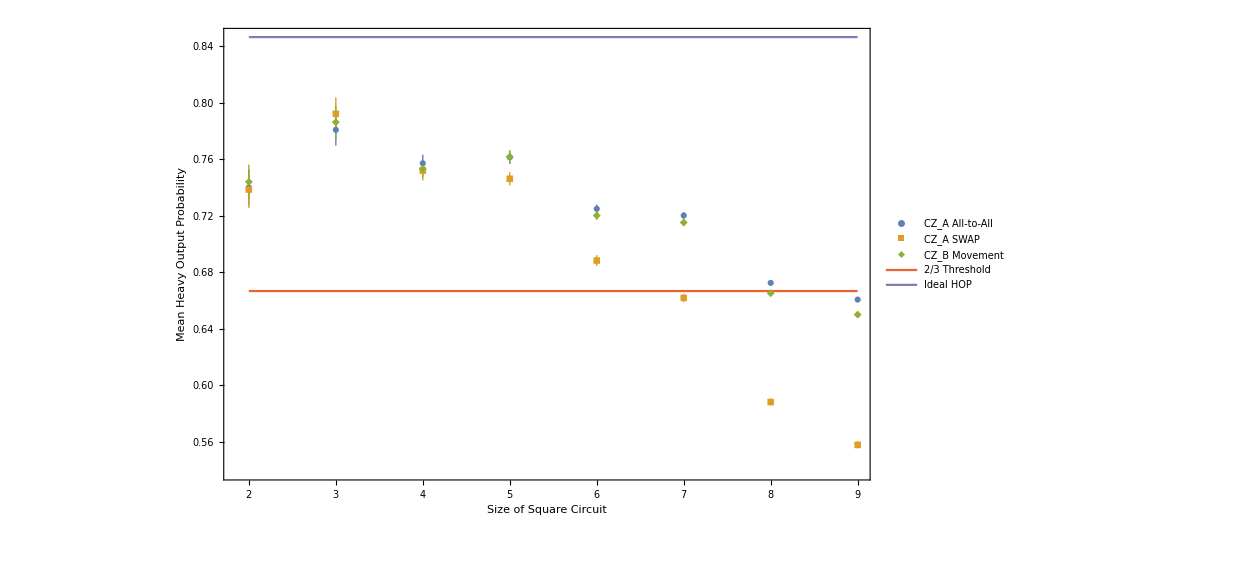

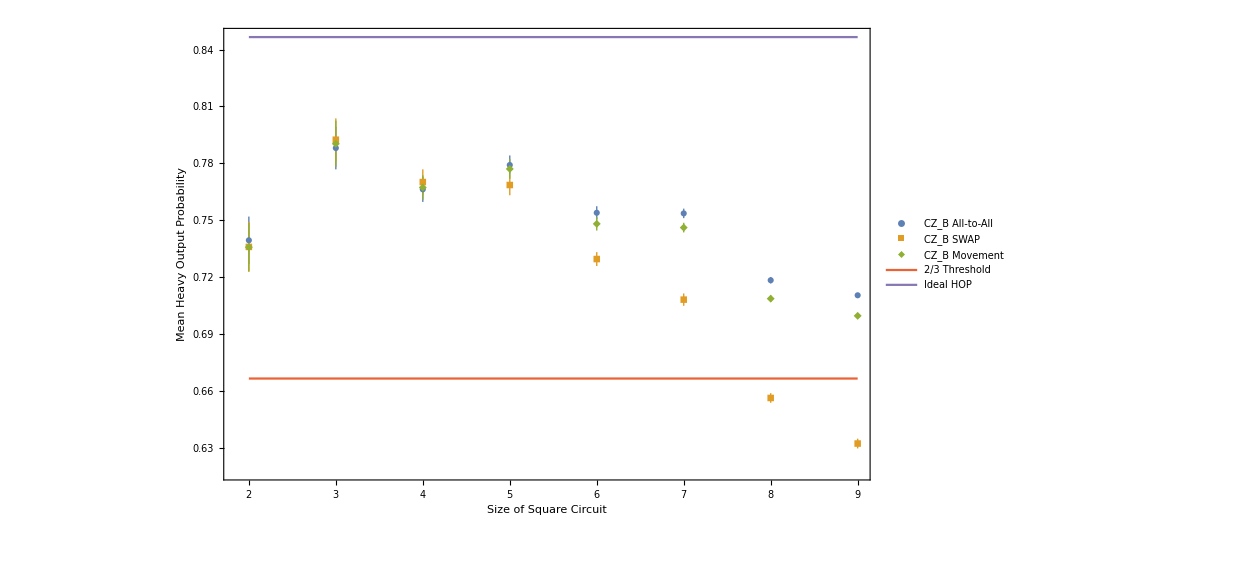

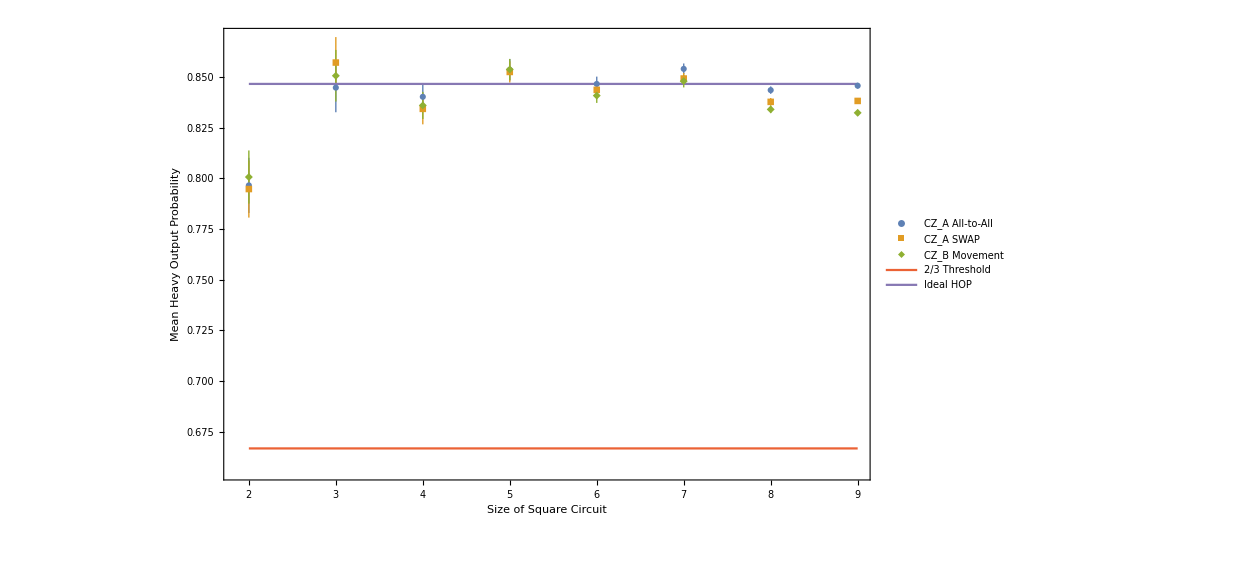

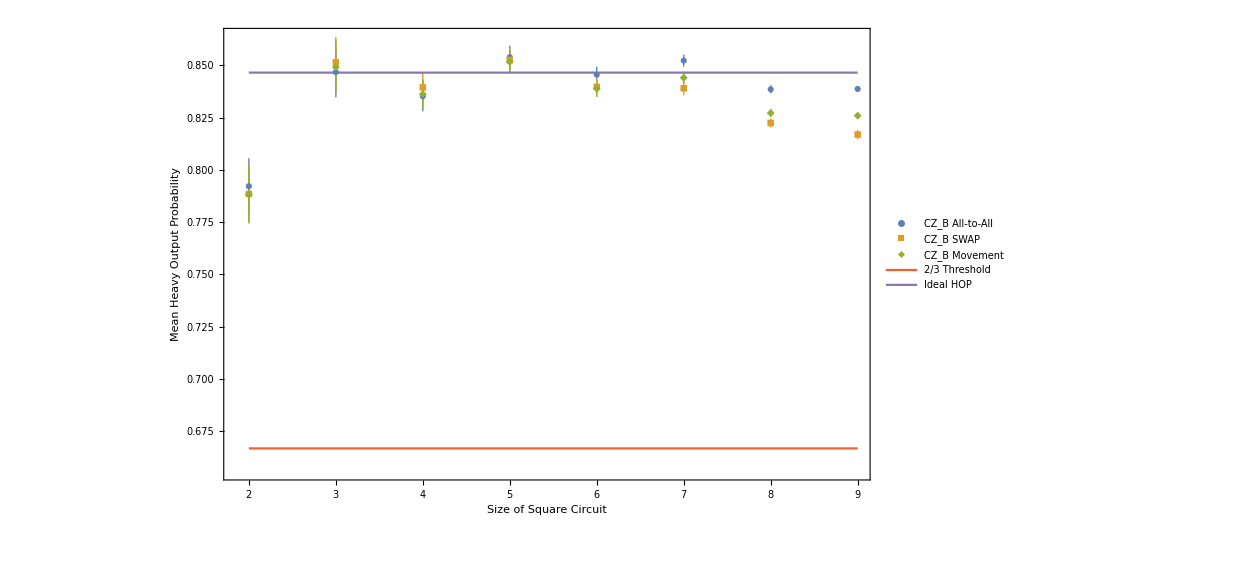

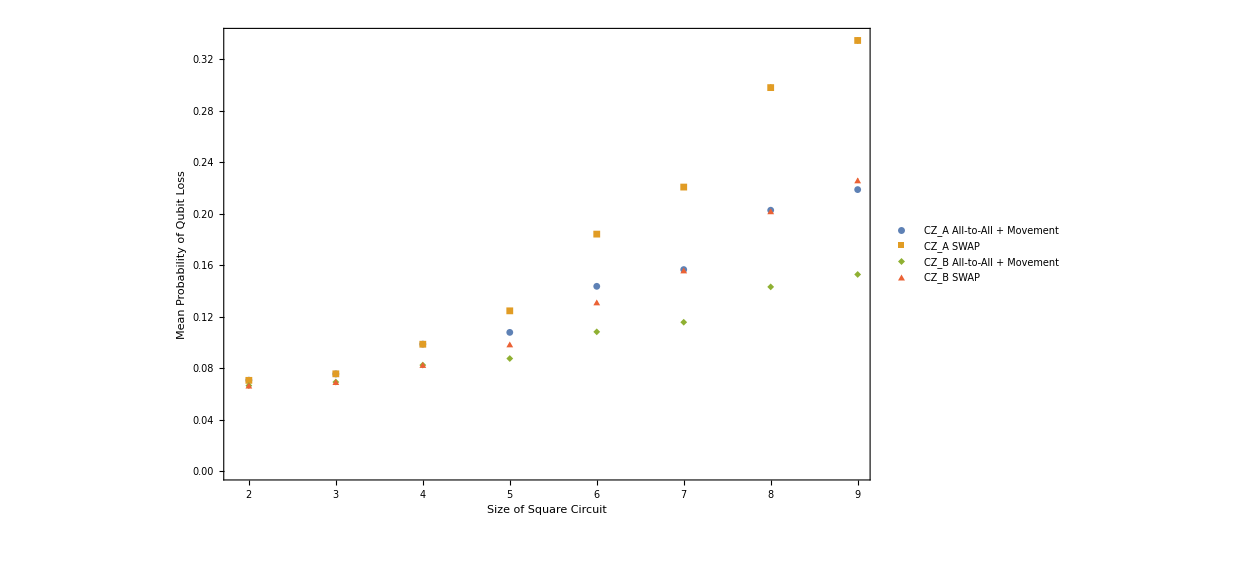

ListLinePlot[{{{2,0.790791±0.0135248},{3,0.848959±0.0119877},{4,0.838436±0.00702298},{5,0.856675±0.0053932},{6,0.850073±0.0038278},{7,0.85422±0.00281338},{8,0.844107±0.00199746},{9,0.845441±0.00139288}},{{2,0.792255±0.0141166},{3,0.847278±0.0124506},{4,0.831176±0.00731335},{5,0.859684±0.00575786},{6,0.846±0.00433786},{7,0.849931±0.00382282},{8,0.837428±0.00375029},{9,0.83543±0.00349307}},{{2,0.797108,0.0128986},{3,0.851692,0.0124526},{4,0.837986,0.00759597},{5,0.855545,0.00517676},{6,0.843309,0.00339957},{7,0.846971,0.00304184},{8,0.832896,0.00208175},{9,0.831794,0.00152376}},{{2,0.789541±0.013737},{3,0.8496±0.0120126},{4,0.834851±0.00702776},{5,0.855517±0.00566381},{6,0.844564±0.00408157},{7,0.851169±0.00298564},{8,0.837976±0.00215053},{9,0.837825±0.0015128}},{{2,0.790255±0.0138441},{3,0.848666±0.0122158},{4,0.838279±0.00670451},{5,0.846128±0.00585462},{6,0.84643±0.00405432},{7,0.839087±0.00371424},{8,0.826037±0.00301181},{9,0.81664±0.00315689}},{{2,0.790255,0.0138441},{3,0.848666,0.0122158},{4,0.838279,0.00670451},{5,0.846128,0.00585462},{6,0.84643,0.00405432},{7,0.839087,0.00371424},{8,0.826037,0.00301181},{9,0.81664,0.00315689}},{{2,2/3},{3,2/3},{4,2/3},{5,2/3},{6,2/3},{7,2/3},{8,2/3},{9,2/3}},{{2,1/2 (1+Log[2])},{3,1/2 (1+Log[2])},{4,1/2 (1+Log[2])},{5,1/2 (1+Log[2])},{6,1/2 (1+Log[2])},{7,1/2 (1+Log[2])},{8,1/2 (1+Log[2])},{9,1/2 (1+Log[2])}}},AxesLabel→{Layer Depth,Heavy Output Generation Probability},Frame→True,FrameLabel→{Size of Square Circuit,Heavy Output Generation Probability},PlotLegends→{Gerard A2A,Gerard SWAP,Harvard A2A,Harvard SWAP,2/3 Threshold,Ideal HOP}]

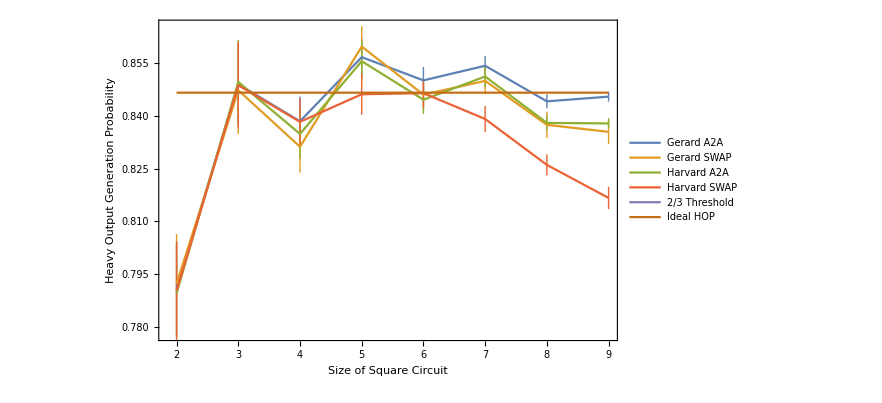

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
ListPlot[{ErrorBars[GA2AQV[[All,1]]],ErrorBars[GSWAPQV[[All,1]]],ErrorBars[GMoveQV[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output  Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_A All-to-All","CZ_A SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Left,Bottom}]]
ListPlot[{ErrorBars[HA2AQV[[All,1]]],ErrorBars[HSWAPQV[[All,1]]],ErrorBars[HMoveQV[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output  Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_B All-to-All","CZ_B SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Left,Bottom}]]


ListPlot[{ErrorBars[GA2AQV[[All,2]]],ErrorBars[GSWAPQV[[All,2]]],ErrorBars[GMoveQV[[All,2]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_A All-to-All","CZ_A SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Right,Center}]]
ListPlot[{ErrorBars[HA2AQV[[All,2]]],ErrorBars[HSWAPQV[[All,2]]],ErrorBars[HMoveQV[[All,2]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Heavy Output Probability"},PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,None,None},Joined->{False,False,False,True,True},PlotLegends->Placed[{"CZ_B All-to-All","CZ_B SWAP","CZ_B Movement","2/3 Threshold","Ideal HOP"},{Right,Center}]]

ListPlot[{ErrorBarsLoss[GA2AQV[[All,3]]],ErrorBarsLoss[GSWAPQV[[All,3]]],ErrorBarsLoss[HA2AQV[[All,3]]],ErrorBarsLoss[HSWAPQV[[All,3]]]},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean Probability of Qubit Loss"},PlotRange->All,PlotMarkers->{Automatic,Small},IntervalMarkers->"Fences",PlotLegends->Placed[{"CZ_A All-to-All + Movement","CZ_A SWAP","CZ_B All-to-All + Movement","CZ_B SWAP"},{Left,Top}]]
```

```mathematica
PlusMinus[1]
```

±1